## Gauge Group Representations

```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->TraditionalForm}]
<<LieArt`
```

LieART 2.0.0

last revised 29 November 2019

### First try! - There is no need to work with LieArt in the final package

```mathematica
GluonsP={{Irrep[SU[3]][8],Irrep[SU[2]][1],0,GGp},{Irrep[SU[3]][1],Irrep[SU[2]][3],0,WWp},{Irrep[SU[3]][1],Irrep[SU[2]][1],0,BBp}}
GluonsM={{Irrep[SU[3]][8],Irrep[SU[2]][1],0,GGm},{Irrep[SU[3]][1],Irrep[SU[2]][3],0,WWm},{Irrep[SU[3]][1],Irrep[SU[2]][1],0,BBm}}
FermionsP={{Irrep[SU[3]][3],Irrep[SU[2]][2],1/6,QQ},{Irrep[SU[3]][Bar[3]],Irrep[SU[2]][1],-2/3,uu},{Irrep[SU[3]][Bar[3]],Irrep[SU[2]][1],1/3,dd},{Irrep[SU[3]][1],Irrep[SU[2]][2],-1/2,LL},{Irrep[SU[3]][1],Irrep[SU[2]][1],1,ee}}
FermionsM={{Irrep[SU[3]][Bar[3]],Irrep[SU[2]][2],-1/6,QBar},{Irrep[SU[3]][3],Irrep[SU[2]][1],2/3,uBar},{Irrep[SU[3]][3],Irrep[SU[2]][1],-1/3,dBar},{Irrep[SU[3]][1],Irrep[SU[2]][2],1/2,LBar},{Irrep[SU[3]][1],Irrep[SU[2]][1],-1,eBar}}
Scalars={{Irrep[SU[3]][1],Irrep[SU[2]][2],1/2,HH},{Irrep[SU[3]][1],Irrep[SU[2]][2],-1/2,HBar}}
Fields={GluonsP,GluonsM,FermionsP,FermionsM,Scalars};
```

(8 | 1 | 0 | GGp
1 | 3 | 0 | WWp
1 | 1 | 0 | BBp)

(8 | 1 | 0 | GGm
1 | 3 | 0 | WWm
1 | 1 | 0 | BBm)

(3 | 2 | 1/6 | QQ
OverBar[3] | 1 | -2/3 | uu
OverBar[3] | 1 | 1/3 | dd
1 | 2 | -1/2 | LL
1 | 1 | 1 | ee)

(OverBar[3] | 2 | -1/6 | QBar
3 | 1 | 2/3 | uBar
3 | 1 | -1/3 | dBar
1 | 2 | 1/2 | LBar
1 | 1 | -1 | eBar)

(1 | 2 | 1/2 | HH
1 | 2 | -1/2 | HBar)

```mathematica
lista={{1,2,3},{4},{5,6},{9,10},{11,12,13,14,15}}
```

{{1,2,3},{4},{5,6},{9,10},{11,12,13,14,15}}

```mathematica
operator8ex={{1,2},{},{3,4},{},{5}}
```

{{1,2},{},{3,4},{},{5}}

```mathematica
LabelsToNumbers[listLabels_List]:=
Module[{listNumbers},
listNumbers=Length/@listLabels;
(*listNumbers[[2]]=listNumbers[[1]]+listNumbers[[2]];
listNumbers=Drop[listNumbers,1];*) (* In the first attempt we did not distinguish between P and M gluons, but it becomes more involved when it comes to assign labels *)
Return[listNumbers];
]
```

```mathematica
lista=LabelsToNumbers[lista]
```

{3,1,2,2,5}

```mathematica
listNumberop8=LabelsToNumbers[operator8ex]
```

{2,0,2,0,1}

```mathematica
ColourSingletDoable[listFields_]:=
Module[{numberFields=Length[listFields],su3=1,su2=1,u1=0},
su3=IrrepMultiplicity[
DecomposeProduct@@
Table[
listFields[[i,1]],
{i,1,numberFields}
],
Irrep[SU[3]][1]
];
su2=IrrepMultiplicity[
DecomposeProduct@@
Table[
listFields[[i,2]],
{i,1,numberFields}
],
Irrep[SU[2]][1]
];
u1=Sum[
listFields[[i,3]],
{i,1,numberFields}
];
If[(su3≥1)&&(su2≥1)&&(u1==0),
Return[CountsToList[listFields]],
Return[Nothing]
]
]
```

```mathematica
(*IsColourSingletDoable[listFields_]:=
Module[{numberFields=Length[listFields],su3=1,su2=1,u1=0,tensors},
su3=IrrepMultiplicity[
DecomposeProduct@@
Table[
listFields[[i,1]],
{i,1,numberFields}
],
Irrep[SU[3]][1]
];
su2=IrrepMultiplicity[
DecomposeProduct@@
Table[
listFields[[i,2]],
{i,1,numberFields}
],
Irrep[SU[2]][1]
];
u1=Sum[
listFields[[i,3]],
{i,1,numberFields}
];
If[(su3≥1)&&(su2≥1)&&(u1==0),
tensors=
Table[
listFields[[i,j]],
{j,1,2},
{i,1,numberFields}
];
Return[tensors],
Return[Nothing]
]
]*)
```

```mathematica
CombinationsOfFields[listNumbers_List]:=
Module[{types=Length[listNumbers],groupingFields},
If[types==5,
groupingFields=
Table[
DeleteDuplicates[
Sort[
Sort/@
Tuples[Fields[[i]],listNumbers[[i]]]
]
],
{i,1,5}];
groupingFields=
ColourSingletDoable/@
Map[
Flatten[#,1]&,
Tuples[groupingFields]
];
Return[groupingFields];
]
]
```

```mathematica
CombinationsOfFields[{2,0,2,0,1}]
```

{CountsToList((1 | 1 | 0 | BBp
1 | 1 | 0 | BBp
1 | 1 | 1 | ee
1 | 2 | -1/2 | LL
1 | 2 | -1/2 | HBar)),CountsToList((1 | 1 | 0 | BBp
1 | 1 | 0 | BBp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((1 | 1 | 0 | BBp
1 | 1 | 0 | BBp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar)),CountsToList((1 | 1 | 0 | BBp
1 | 3 | 0 | WWp
1 | 1 | 1 | ee
1 | 2 | -1/2 | LL
1 | 2 | -1/2 | HBar)),CountsToList((1 | 1 | 0 | BBp
1 | 3 | 0 | WWp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((1 | 1 | 0 | BBp
1 | 3 | 0 | WWp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar)),CountsToList((1 | 1 | 0 | BBp
8 | 1 | 0 | GGp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((1 | 1 | 0 | BBp
8 | 1 | 0 | GGp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar)),CountsToList((1 | 3 | 0 | WWp
1 | 3 | 0 | WWp
1 | 1 | 1 | ee
1 | 2 | -1/2 | LL
1 | 2 | -1/2 | HBar)),CountsToList((1 | 3 | 0 | WWp
1 | 3 | 0 | WWp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((1 | 3 | 0 | WWp
1 | 3 | 0 | WWp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar)),CountsToList((1 | 3 | 0 | WWp
8 | 1 | 0 | GGp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((1 | 3 | 0 | WWp
8 | 1 | 0 | GGp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar)),CountsToList((8 | 1 | 0 | GGp
8 | 1 | 0 | GGp
1 | 1 | 1 | ee
1 | 2 | -1/2 | LL
1 | 2 | -1/2 | HBar)),CountsToList((8 | 1 | 0 | GGp
8 | 1 | 0 | GGp
OverBar[3] | 1 | -2/3 | uu
3 | 2 | 1/6 | QQ
1 | 2 | 1/2 | HH)),CountsToList((8 | 1 | 0 | GGp
8 | 1 | 0 | GGp
OverBar[3] | 1 | 1/3 | dd
3 | 2 | 1/6 | QQ
1 | 2 | -1/2 | HBar))}

```mathematica
(*StructuresOfFields[listNumbers_List]:=
Module[{types=Length[listNumbers],groupingFields},
If[types==4,
groupingFields=
Table[
DeleteDuplicates[
Sort[
Sort/@
Tuples[Fields[[i]],listNumbers[[i]]]
]
],
{i,1,4}];
groupingFields=
IsColourSingletDoable/@
Map[
Flatten[#,1]&,
Tuples[groupingFields]
];
Return[groupingFields];
]
]*)
```

```mathematica
CombinationsOfFields[{1,0,0,0,6}]
```

{CountsToList((1 | 1 | 0 | BBp
1 | 2 | -1/2 | HBar
1 | 2 | -1/2 | HBar
1 | 2 | -1/2 | HBar
1 | 2 | 1/2 | HH
1 | 2 | 1/2 | HH
1 | 2 | 1/2 | HH)),CountsToList((1 | 3 | 0 | WWp
1 | 2 | -1/2 | HBar
1 | 2 | -1/2 | HBar
1 | 2 | -1/2 | HBar
1 | 2 | 1/2 | HH
1 | 2 | 1/2 | HH
1 | 2 | 1/2 | HH))}

```mathematica
SMEFTOperatorDoable[{helicityStructures_,listLabels_List,numberDerivatives_Integer}]:=
Module[{listNumbers=LabelsToNumbers[listLabels],combinations,numberCombinations,operators},
combinations=CombinationsOfFields[listNumbers];
numberCombinations=Length[combinations];
operators=
Table[
{helicityStructures,listLabels,numberDerivatives,combinations[[i]]},
{i,1,numberCombinations}
]
]
```

```mathematica
Flatten[SMEFTOperatorDoable/@(MatterContentStrucutures[#,8]&/@operator8ind),1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[operator8ind,1].

```mathematica
(*IsSMEFTOperatorDoable[{helicityStructures_,listLabels_List,numberDerivatives_Integer}]:=
Module[{listNumbers=LabelsToNumbers[listLabels],combinations,numberCombinations,operators},
combinations=StructuresOfFields[listNumbers];
numberCombinations=Length[combinations];
operators=
Table[
{helicityStructures,listLabels,numberDerivatives,combinations[[i]]},
{i,1,numberCombinations}
]
]*)
```

### Some tests of the functions in the LieArt Package

```mathematica
Table[
IrrepMultiplicity[
DecomposeProduct[
Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1]
],Irrep[SU[n]][1]
],{n,2,6}]
```

{6,32,43,44,44}

```mathematica
Binomial[5,4]
```

5

```mathematica
ProductRep[l_,m_,n_]:=Join[Table[Irrep[SU[n]][n^2-1],{i,1,l}],Table[Irrep[SU[n]][n],{i,1,m}],Table[Irrep[SU[n]][If[n==2,n,Bar[n]]],{i,1,m}]]
```

```mathematica
ProductRep[5,0,4]
```

{15,15,15,15,15}

```mathematica
NumberOfSinglets[l_,m_,n_]:=
If[
ProductRep[l,m,n]=={},
1,
If[Length[ProductRep[l,m,n]]==1,(*ProductRep[1,0,n] contatins only the adjoint and DecomposeProduct do not act on it*)
0,
IrrepMultiplicity[
DecomposeProduct@@ProductRep[l,m,n],
Irrep[SU[n]][1]
]
]
]
```

```mathematica
NumberOfSinglets[0,7,4]
```

4582

```mathematica
F[m_,n_]:=(m+n)!-Sum[Binomial[m,i]F[m-i,n],{i,1,m}]
```

```mathematica
F[0,7]
```

5040

```mathematica
FF[m_,n_]:=
If[n==0,
(m)!-Sum[Binomial[m,i]FF[m-i,0],{i,1,m}],
Sum[Binomial[n,i]*FF[m+i,0],{i,0,n}]
]
```

```mathematica
Table[F[m,n],{n,0,6},{m,0,6}];
MatrixForm[%]
```

(1 | 0 | 1 | 2 | 9 | 44 | 265
1 | 1 | 3 | 11 | 53 | 309 | 2119
2 | 4 | 14 | 64 | 362 | 2428 | 18806
6 | 18 | 78 | 426 | 2790 | 21234 | 183822
24 | 96 | 504 | 3216 | 24024 | 205056 | 1965624
120 | 600 | 3720 | 27240 | 229080 | 2170680 | 22852200
720 | 4320 | 30960 | 256320 | 2399760 | 25022880 | 287250480)

```mathematica
Table[F[m,0],{m,0,10}]
Table[N[F[m,0]/m!,1],{m,0,10}]
```

{1,0,1,2,9,44,265,1854,14833,133496,1334961}

{1.,0,0.5,0.3,0.4,0.4,0.4,0.4,0.4,0.4,0.4}

```mathematica
Table[F[i,0]-NumberOfSinglets[i,0,3],{i,0,7}]
Table[N[(F[i,0]-NumberOfSinglets[i,0,3])/i!,1],{i,0,9}]
```

{0,0,0,0,1,12,120,1152}

{0,0,0,0,0.04,0.1,0.2,0.2,0.3,0.3}

```mathematica
factor[n_]:=Sum[Binomial[n-4,i]*(n-i)!/4!*(-1)^i,{i,0,n-4}]
constraints[n_]:=Binomial[n,4]*factor[n]
```

```mathematica
Table[Sum[Binomial[n-4,i]*factor[n-i],{i,0,n}]*4!/n!,{n,4,30}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
factor[8]
Table[N[constraints[m]/(m^4*m!),1],{m,20,40}]
```

1001

{0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006}

```mathematica
Table[F[i+2,0]-NumberOfSinglets[i+2,0,i],{i,2,6}]
```

{6,12,20,30,42}

```mathematica
NumberOfSinglets[6,0,3]
```

145

```mathematica
F[6,0]
```

265

```mathematica
RestrictedConstraints[n_]:=Binomial[n,4]
Table[RestrictedConstraints[i],{i,1,10}]
```

{0,0,0,1,5,15,35,70,126,210}

```mathematica
TotalNumberConstraints[n_]:=Binomial[n,4]*n!/4!
Table[TotalNumberConstraints[i],{i,1,10}]
```

{0,0,0,1,25,450,7350,117600,1905120,31752000}

```mathematica
FFF[m_]:=Sum[Power[-1,i]*m!/i!,{i,0,m}]
```

```mathematica
Table[Sum[Binomial[m,i]*FFF[m-i],{i,0,m}]/m!,{m,0,10}]
```

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[FFF[m]-FF[m,0],{m,0,10}]
```

{0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[F[6-i,i]-NumberOfSinglets[6-i,i,3],{i,0,6}]
```

{120,132,145,159,174,190,207}

```mathematica
Table[NumberOfSinglets[m,0,3],{m,0,8}]
```

{1,0,1,2,8,32,145,702,3598}

```mathematica
FactorInteger[145]
```

(5 | 1
29 | 1)

```mathematica
FactorInteger/@%
```

((5 | 1) | (1 | 1)
(29 | 1) | (1 | 1))

```mathematica
Table[F[m,0]-NumberOfSinglets[m,0,2],{m,0,10}]
FactorInteger/@%
```

{0,0,0,1,6,38,250,1818,14742,133264,1334358}

{(0 | 1),(0 | 1),(0 | 1),(1 | 1),(2 | 1
3 | 1),(2 | 1
19 | 1),(2 | 1
5 | 3),(2 | 1
3 | 2
101 | 1),(2 | 1
3 | 4
7 | 1
13 | 1),(2 | 4
8329 | 1),(2 | 1
3 | 2
74131 | 1)}

```mathematica
NumberOfSinglets[4,1,3]
```

40

```mathematica
F[4,1]
```

53

```mathematica
DimY[m_,n_]:=If[
(m≥n)&&(n≥0),
(m+2)*(n+1)*(m-n+1)/2,
0
]
```

```mathematica
ProductAdjoint[m_,n_]:=
If[m≥n,
If[n≥0,
DimY[m+2,n+1]+DimY[m+1,n+2]+If[m≥n+1,DimY[m,n],0]+DimY[m-1,n+1],
0]+
If[
n≥1,
DimY[m+1,n-1]+DimY[m,n]+DimY[m-2,n-1],
0]+
If[
n≥2,
DimY[m-1,n-2],
0],
0]
```

```mathematica
Table[DimY[m,n]*8==ProductAdjoint[m,n],{n,0,10},{m,0,10}];
MatrixForm[%]
```

(True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True)

```mathematica
NotSU3Rep[{m_Integer,n_Integer}]:=
If[(n>m)||(m<0)||(n<0),Return[Nothing],Return[{m,n}]]
```

```mathematica
TimesAdjoint[{m_Integer,n_Integer}]:=
NotSU3Rep/@
Join[
If[n≥0,{{m+2,n+1},{m+1,n+2},If[m≥n+1,{m,n},Nothing],{m-1,n+1}},{}],
If[n≥1,{{m+1,n-1},{m,n},{m-2,n-1}},{}],
If[n≥2,{{m-1,n-2}},{}]
]
```

```mathematica
TimesAdjoint[{2,1}]
```

(4 | 2
3 | 3
2 | 1
3 | 0
2 | 1
0 | 0)

```mathematica
TimesAdjoint[{0,0}]
```

(2 | 1)

```mathematica
TensorOfAdjontRepresentations[n_Integer]:=
If[n>0,
Module[{tensorproduct={{2,1}}},
For[i=1,i<n,i++,
tensorproduct=Sort[Flatten[TimesAdjoint/@tensorproduct,1]];
];
Return[tensorproduct]
],
Return[{0,0}]
]
```

```mathematica
Flatten[TimesAdjoint/@{{2,1}},1]
TimesAdjoint/@%
```

(4 | 2
3 | 3
2 | 1
3 | 0
2 | 1
0 | 0)

{(6 | 3
5 | 4
4 | 2
3 | 3
5 | 1
4 | 2
2 | 1
3 | 0),(5 | 4
4 | 2
3 | 3
2 | 1),(4 | 2
3 | 3
2 | 1
3 | 0
2 | 1
0 | 0),(5 | 1
4 | 2
3 | 0
2 | 1),(4 | 2
3 | 3
2 | 1
3 | 0
2 | 1
0 | 0),(2 | 1)}

```mathematica
Table[Counts[TensorOfAdjontRepresentations[i]],{i,1,8}];
MatrixForm[%]
```

(<|{2,1}→1|>
<|{0,0}→1,{2,1}→2,{3,0}→1,{3,3}→1,{4,2}→1|>
<|{0,0}→2,{2,1}→8,{3,0}→4,{3,3}→4,{4,2}→6,{5,1}→2,{5,4}→2,{6,3}→1|>
<|{0,0}→8,{2,1}→32,{3,0}→20,{3,3}→20,{4,2}→33,{5,1}→15,{5,4}→15,{6,0}→2,{6,3}→12,{6,6}→2,{7,2}→3,{7,5}→3,{8,4}→1|>
<|{0,0}→32,{2,1}→145,{3,0}→100,{3,3}→100,{4,2}→180,{5,1}→100,{5,4}→100,{6,0}→20,{6,3}→94,{6,6}→20,{7,2}→36,{7,5}→36,{8,1}→5,{8,4}→20,{8,7}→5,{9,3}→4,{9,6}→4,{10,5}→1|>
<|{0,0}→145,{2,1}→702,{3,0}→525,{3,3}→525,{4,2}→999,{5,1}→630,{5,4}→630,{6,0}→161,{6,3}→660,{6,6}→161,{7,2}→315,{7,5}→315,{8,1}→70,{8,4}→215,{8,7}→70,{9,0}→5,{9,3}→70,{9,6}→70,{9,9}→5,{10,2}→9,{10,5}→30,{10,8}→9,{11,4}→5,{11,7}→5,{12,6}→1|>
<|{0,0}→702,{2,1}→3598,{3,0}→2856,{3,3}→2856,{4,2}→5670,{5,1}→3920,{5,4}→3920,{6,0}→1176,{6,3}→4424,{6,6}→1176,{7,2}→2436,{7,5}→2436,{8,1}→700,{8,4}→1890,{8,7}→700,{9,0}→84,{9,3}→784,{9,6}→784,{9,9}→84,{10,2}→168,{10,5}→426,{10,8}→168,{11,1}→14,{11,4}→120,{11,7}→120,{11,10}→14,{12,3}→14,{12,6}→42,{12,9}→14,{13,5}→6,{13,8}→6,{14,7}→1|>
<|{0,0}→3598,{2,1}→19280,{3,0}→16044,{3,3}→16044,{4,2}→32914,{5,1}→24402,{5,4}→24402,{6,0}→8232,{6,3}→29120,{6,6}→8232,{7,2}→17766,{7,5}→17766,{8,1}→6048,{8,4}→15070,{8,7}→6048,{9,0}→966,{9,3}→7308,{9,6}→7308,{9,9}→966,{10,2}→2052,{10,5}→4592,{10,8}→2052,{11,1}→294,{11,4}→1680,{11,7}→1680,{11,10}→294,{12,0}→14,{12,3}→336,{12,6}→763,{12,9}→336,{12,12}→14,{13,2}→28,{13,5}→189,{13,8}→189,{13,11}→28,{14,4}→20,{14,7}→56,{14,10}→20,{15,6}→7,{15,9}→7,{16,8}→1|>)

```mathematica
TimesAdjoint[{3,0}]
```

(5 | 1
4 | 2
3 | 0
2 | 1)

```mathematica
DecomposeProduct[Irrep[SU[3]][8],Irrep[SU[3]][8],Irrep[SU[3]][8],Irrep[SU[3]][8]]
```

8(1)+32(8)+20(10)+20(OverBar[10])+33(27)+2(28)+2(OverBar[28])+15(35)+15(OverBar[35])+12(64)+3(81)+3(OverBar[81])+125

```mathematica
DecomposeProduct[Irrep[SU[3]][3],Irrep[SU[3]][8]]
```

3+OverBar[6]+15

```mathematica
IrrepMultiplicity[%,Irrep[SU[3]][1]]
```

0

```mathematica
Table[
IrrepMultiplicity[
DecomposeProduct[
Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1]
],Irrep[SU[n]][1]
],{n,2,15}]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Column[
Table[
IrrepMultiplicity[
DecomposeProduct[
Sequence@@Table[Irrep[SU[3]][8],{m,1,n}]
],
Irrep[SU[3]][1]],
{n,1,8}
]
]
```

IrrepMultiplicity({8},1)
1
2
8
32
145
702
3598

```mathematica
MatrixForm[
Table[
DecomposeProduct[
Irrep[SU[n]][n^2-1],Irrep[SU[n]][n^2-1]],
{n,2,12}]
]
```

(1+3+5
1+2(8)+10+OverBar[10]+27
1+2(15)+20'+45+OverBar[45]+84
1+2(24)+75+126+OverBar[126]+200
1+2(35)+189+280+OverBar[280]+405
1+2(48)+392+540+OverBar[540]+735'
1+2(63)+720+945+OverBar[945]+1232
1+2(80)+1215+1540+OverBar[1540]+1944
1+2(99)+1925+2376+OverBar[2376]+2925
1+2(120)+2904+3510+OverBar[3510]+4235
1+2(143)+4212+5005+OverBar[5005]+5940)

```mathematica
(n^2-1)^2-2*(n^2-1)-1//Simplify//Factor
```

n^4-4 n^2+2

```mathematica
YoungTableau[Irrep[SU[5]][200]]
```

|  |  | 
 |  |  | 
 |  |  | 
 |  |  |

```mathematica
YoungTableau[Irrep[SU[6]][280]]
```

|  | 
 |  | 
 |  | 
 |  | 
 |  |

```mathematica
YoungTableau[Irrep[SU[7]][392]]
```

| 
 | 
 | 
 | 
 | 
 |

```mathematica
MatrixForm[
Table[
DecomposeProduct[
Irrep[SU[n]][n],Irrep[SU[n]][n],Irrep[SU[n]][n]],
{n,3,10}]
]
```

(1+2(8)+10
OverBar[4]+2(OverBar[20])+OverBar[20]''
OverBar[10]+OverBar[35]+2(OverBar[40])
20+56+2(70)
35+84+2(112)
56+120+2(168)
84+165+2(240)
120+220+2(330))

```mathematica
IrrepMultiplicity[
DecomposeProduct[
Irrep[SU[2]][2],Irrep[SU[2]][2],Irrep[SU[2]][2],Irrep[SU[2]][2],Irrep[SU[2]][2],Irrep[SU[2]][2]],
Irrep[SU[2]][1]]
```

5

```mathematica
Table[
IrrepMultiplicity[
DecomposeProduct[
Irrep[SU[n]][n],Irrep[SU[n]][n],Irrep[SU[n]][n],Irrep[SU[n]][Bar[n]],Irrep[SU[n]][Bar[n]],Irrep[SU[n]][Bar[n]]],
Irrep[SU[n]][1]],
{n,3,15}
]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
CasimirInvariant[Irrep[SU[3]][8]]
```

3

## SU(3) invariants through graphs - I did not find an emerging pattern in the graph for the SU(3) invariants! Important observation: up to dimension 9, only 4 adjoint structures can appear at maximum, so a general rule is not needed!

```mathematica
(*I need to generate all the oriented graphs with n points and each of these has a line going out and a line coming in. The fastest route is generating its adjacency matrix first.*)
```

```mathematica
(*IsDuplicateFree[lines_List]:=
If[
DuplicateFreeQ[lines],
Return[lines],
Return[Nothing]
]*)
```

```mathematica
IsTrueAdjoint[lines_List]:=
If[
Diagonal[lines]==Table[0,Length[lines]],
Return[lines],
Return[Nothing]
]
```

```mathematica
(*AdjacencyMatricesSUN[n_]:=
IsTrueAdjoint/@
IsDuplicateFree/@
Tuples[Permutations[PadRight[{1},n]],n]*)
```

```mathematica
AdjacencyMatricesSU3[n_]:=
IsTrueAdjoint/@
Permutations[Permutations[PadRight[{1},n]]] (*no comperison in speed with the previous one*)
```

```mathematica
AdjacencyMatricesSU3[9]//Length//Timing
```

{1.43021,133496}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}],DirectedEdges->True]&/@AdjacencyMatricesSU3[5];
```

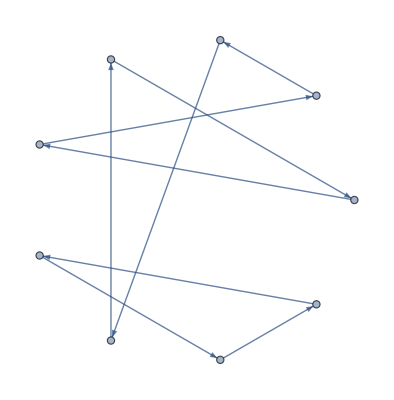

```mathematica
AdjacencyGraph[AdjacencyMatricesSU3[9][[10000]],VertexCoordinates->ellipseLayout[9,{1,1}],DirectedEdges->True]
```

```mathematica
ZeroDiagonal[matrix_List]:=
Module[{newmatrix=matrix},
Do[
newmatrix[[i,i]]=0,
{i,1,Length[matrix]}
];
Return[newmatrix];
]
```

```mathematica
UpperTriangularAdjacencyMatrix[n_,int_]:=UpperTriangularize[Table[RandomInteger[{0,int}],n,n],1]
```

```mathematica
SymmetricAdjacencyMatrix[n_,int_]:=
Module[{upper=UpperTriangularAdjacencyMatrix[n,int]},
Return[upper+Transpose[upper]];
]
DirectedAdjacencyMatrix[n_,int_]:=
Module[{upper=Table[RandomInteger[{0,int}],n,n]},
Return[ZeroDiagonal[upper]];
]
```

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0)

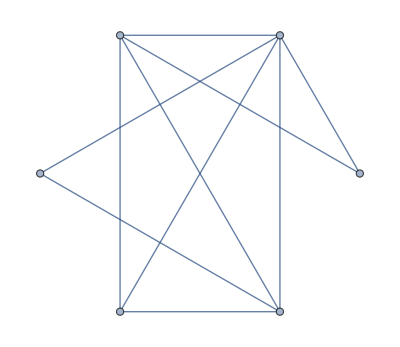

```mathematica
mat=SymmetricAdjacencyMatrix[6,1];
mat//MatrixForm
AdjacencyGraph[mat,VertexCoordinates->ellipseLayout[6,{1,1}]]
```

```mathematica
EdgeList[AdjacencyGraph[mat]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->4,2<->5,2<->6,3<->5,4<->5}

```mathematica
dirmat=DirectedAdjacencyMatrix[6,1];
dirmat//MatrixForm
AdjacencyGraph[dirmat,VertexCoordinates->ellipseLayout[6,{1,1}]]
```

(0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0)

-Graphics-

```mathematica
EdgeList[AdjacencyGraph[dirmat]]
```

{1->2,1->5,1->6,2->5,2->6,3->2,3->4,3->5,3->6,4->2,4->3,4->5,4->6,5->6,6->1,6->3,6->5}

```mathematica
TotalCrossingCount[adjacencymatrix_List]:=
Module[{matrixdim=Length[adjacencymatrix],i,j, crossings=0,transpose=Transpose[adjacencymatrix]},
For[i=1,i≤matrixdim,i++,
For[j=i+2,j≤matrixdim-1,j++,
If[
adjacencymatrix[[i,j]]≠0,
crossings=crossings+adjacencymatrix[[i,j]]*Sum[adjacencymatrix[[k,l]],{k,i+1,j-1},{l,j+1,matrixdim}](*+Sum[transpose[[k,l]],{k,i+1,j-1},{l,j+1,matrixdim}]*)
]
]
];
(*For[i=1,i≤matrixdim,i++,
For[j=i+2,j≤matrixdim-1,j++,
If[
transpose[[i,j]]≠0,
crossings=crossings+Sum[adjacencymatrix[[k,l]],{k,i+1,j-1},{l,j+1,matrixdim}]+Sum[transpose[[k,l]],{k,i+1,j-1},{l,j+1,matrixdim}]
]
]
];*)
Return[crossings];
]
```

```mathematica
TotalCrossingCount[mat]
```

8

```mathematica
UndirectedEdgeCrossingCount[adjacencymatrix_List,UndirectedEdge[row_,column_]]:=
Module[{matrixdim=Length[adjacencymatrix],crossings},
If[adjacencymatrix[[row,column]]≠0,
crossings=Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,column+1,matrixdim}]+Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,1,row-1}],
crossings=0
]
]
```

```mathematica
UndirectedEdgeCrossingCount[mat,#]&/@EdgeList[AdjacencyGraph[mat]]
```

{0,3,3,1,0,2,2,3,2,0}

```mathematica
DirectedEdgeCrossingCount[adjacencymatrix_List,DirectedEdge[i_,j_]]:=
Module[{matrixdim=Length[adjacencymatrix],crossingsL=0,crossingsR=0,row=i,column=j,transpose=Transpose[adjacencymatrix] },
If[
adjacencymatrix[[i,j]]≠0&&(i>j+1||j>i+1),
If[i>j+1,
column=i;
row=j;
crossingsR=Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,column+1,matrixdim}]+Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,1,row-1}];
crossingsL=Sum[transpose[[k,l]],{k,row+1,column-1},{l,column+1,matrixdim}]+Sum[transpose[[k,l]],{k,row+1,column-1},{l,1,row-1}],
crossingsL=Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,column+1,matrixdim}]+Sum[adjacencymatrix[[k,l]],{k,row+1,column-1},{l,1,row-1}];
crossingsR=Sum[transpose[[k,l]],{k,row+1,column-1},{l,column+1,matrixdim}]+Sum[transpose[[k,l]],{k,row+1,column-1},{l,1,row-1}];
];
];
Return[{crossingsL,crossingsR}];
]
```

```mathematica
DirectedEdgeCrossingCount[dirmat,DirectedEdge[2,4]]
```

{0,0}

```mathematica
DirectedEdgeCrossingCount[dirmat,#]&/@EdgeList[AdjacencyGraph[dirmat]]
```

{{0,0},{3,1},{0,0},{2,1},{0,1},{0,0},{0,0},{2,0},{1,2},{1,2},{0,0},{0,0},{0,3},{0,0},{0,0},{2,1},{0,0}}

```mathematica
PermutationsSubset[list_List,subsetpositions_List]:=
Module[{subset=Table[list[[i]],{i,subsetpositions}],subsetpermutations,permutations},
subsetpermutations=Permutations[subset];
permutations=
Table[
If[
MemberQ[subsetpositions,j],
subsetpermutations[[i,Position[subsetpositions,j][[1,1]]]],
list[[j]]
],
{i,1,Length[subsetpermutations]},{j,1,Length[list]}
]
]
```

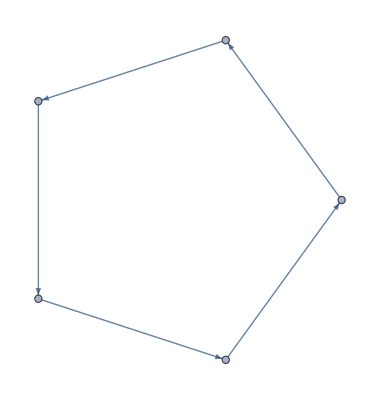
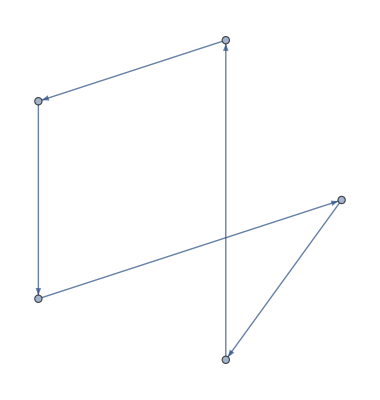
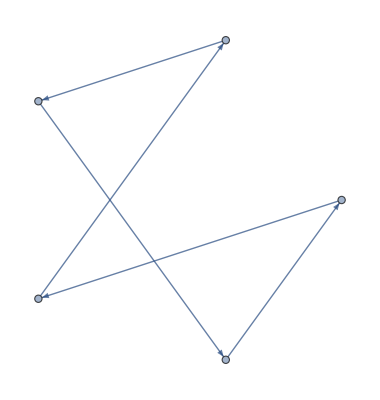
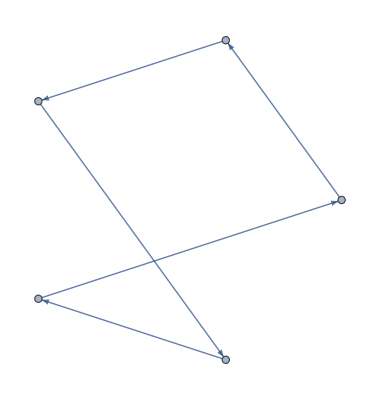
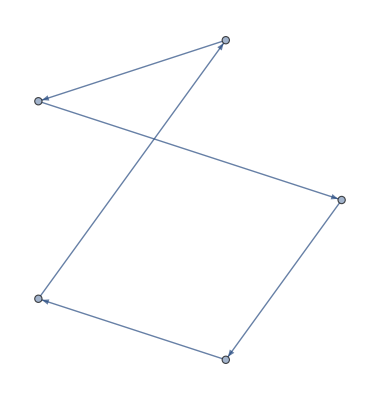
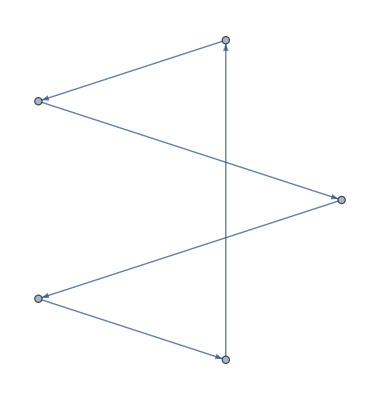
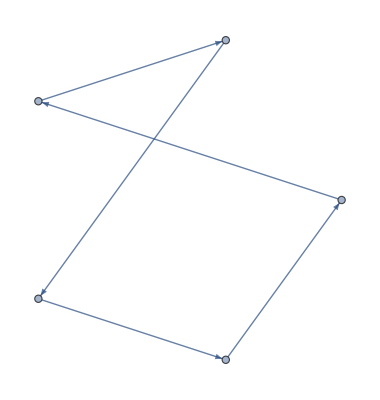
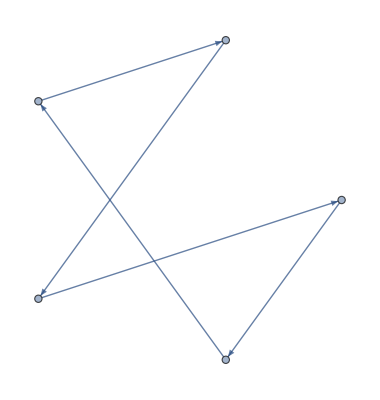
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}],DirectedEdges->True]&/@AdjacencyMatricesSU3[5]
```

```mathematica
Do[Print[AdjacencyGraph[#,VertexCoordinates->ellipseLayout[5,{1,1}],DirectedEdges->True]&/@(IsTrueAdjoint/@PermutationsSubset[AdjacencyMatricesSU3[5][[i]],{1,2,3,5}])],{i,1,44}];
```

AdjacencyGraph::matsq: Argument IsTrueAdjoint(5) at position 2 is not a non-empty square matrix.

AdjacencyGraph::matsq: Argument IsTrueAdjoint({1,2,3,5}) at position 2 is not a non-empty square matrix.

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(5),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

Part::partw: Part 2 of AdjacencyMatricesSU3(5) does not exist.

AdjacencyGraph::matsq: Argument IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦2⟧) at position 2 is not a non-empty square matrix.

General::stop: Further output of AdjacencyGraph::matsq will be suppressed during this calculation.

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦2⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

Part::partw: Part 3 of AdjacencyMatricesSU3(5) does not exist.

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦3⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

Part::partw: Part 4 of AdjacencyMatricesSU3(5) does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦4⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦5⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦6⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦7⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦8⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦9⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦10⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦11⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦12⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦13⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦14⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦15⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦16⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦17⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦18⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦19⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦20⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦21⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦22⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦23⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦24⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦25⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦26⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦27⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦28⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦29⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦30⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦31⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦32⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦33⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦34⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦35⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦36⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦37⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦38⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦39⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦40⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦41⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦42⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦43⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

PermutationsSubset(AdjacencyGraph[Automatic,IsTrueAdjoint(AdjacencyMatricesSU3(5)⟦44⟧),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True],AdjacencyGraph[Automatic,IsTrueAdjoint({1,2,3,5}),VertexCoordinates→ellipseLayout(5,{1,1}),DirectedEdges→True])

```mathematica
CountMultipleIntersections[adjacencymatrix_List]:=
Module[{crossings,counting=0},
crossings=DirectedEdgeCrossingCount[adjacencymatrix,#]&/@EdgeList[AdjacencyGraph[adjacencymatrix,DirectedEdges->True]];
Do[
If[
crossings[[i,1]]≠0&&crossings[[i,2]]≠0,
counting+=1
],
{i,1,Length[crossings]}];
If[counting≥4,
Return[adjacencymatrix],
Return[Nothing]
]
]
```

```mathematica
AdjacencyGraph[#,VertexCoordinates->ellipseLayout[6,{1,1}],DirectedEdges->True]&/@(CountMultipleIntersections/@AdjacencyMatricesSU3[6]);
```

```mathematica
(*AntiSymmetrisationMatrix[matrix_List,tobepermuted_List]:=
Module[{permutedrows,permutedmatrices},

permutedrows=
Permutations[
Table[matrix[[i]],{i,tobepermuted}]
];

Print[permutedrows];

Do[
permutedmatrices[[n]]=
Table[
If[
MemberQ[i,tobepermuted],
permutedrows[[n,i]],
matrix[[i]]
],
{i,1,Length[matrix]}
];
Print[permutedmatrices[[n]]];,
{n,1,Length[permutedrows]}
];

permutedmatrices=IsTrueAdjoint/@permutedmatrices;

Return[permutedmatrices];

]*)(*this function is not very usefull since a big role is played for sure by the relative signs when you apply an antisymmetrisation, substitution (on one of the resulting terms) and antisymmetrisation again*)
```

```mathematica
(*SubMatrix[matrix_List,{rows_List,columns_List}]:=
Module[{submatrix},
submatrix=
Transpose[
Delete[
Transpose[
Delete[matrix,rows]
],
columns
]
]
]*)
```

```mathematica
(*ColumnsAndRows[dimension_,subdimension_]:=
Module[{toeliminate=dimension-subdimension,labels=Table[{i},{i,1,dimension}],rowsandcolumns},
rowsandcolumns=
DeleteDuplicates[
Sort/@
IsDuplicateFree/@
Tuples[labels,toeliminate]];
rowsandcolumns=Tuples[{rowsandcolumns,rowsandcolumns}];
Return[rowsandcolumns];
]*)
```

```mathematica
(*antidiagonal={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}*)
```

```mathematica
(*IsTheMatrixOK[matrix_List]:=If[
MemberQ[
(SubMatrix[matrix,#]&/@ColumnsAndRows[Length[matrix],4]),
antidiagonal
],
Return[Nothing],
Return[matrix]
]*)
```

```mathematica
(*MatrixForm/@(IsTheMatrixOK/@AdjacencyMatricesSU3[5])*)
```

```mathematica
IsTrueAdjoint2[list_List]:=
Module[{numberpoints=Length[list]},
For[i=1,i≤numberpoints,i++,
If[
i==list[[i]],
Return[Nothing]
]
];
Return[list];
]
```

```mathematica
AllEdges[n_]:=
Module[{edges=Table[i,{i,1,n}]},
edges=Permutations[edges];
Return[edges];
]
```

```mathematica
AllEdgesAdjoint[n_]:=
Module[{edges=Table[i,{i,1,n}]},
edges=IsTrueAdjoint2/@Permutations[edges];
Return[edges];
]
```

```mathematica
(IsTrueAdjoint2/@PermutationsSubset[AllEdges[4][[1]],{1,2,3,4}])
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

```mathematica
IsTrueAdjoint2[{1,3,4,2}]
```

Nothing

```mathematica
AllEdges[5]
```

{{1,2,3,4,5},{1,2,3,5,4},{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4},{1,2,5,4,3},{1,3,2,4,5},{1,3,2,5,4},{1,3,4,2,5},{1,3,4,5,2},{1,3,5,2,4},{1,3,5,4,2},{1,4,2,3,5},{1,4,2,5,3},{1,4,3,2,5},{1,4,3,5,2},{1,4,5,2,3},{1,4,5,3,2},{1,5,2,3,4},{1,5,2,4,3},{1,5,3,2,4},{1,5,3,4,2},{1,5,4,2,3},{1,5,4,3,2},{2,1,3,4,5},{2,1,3,5,4},{2,1,4,3,5},{2,1,4,5,3},{2,1,5,3,4},{2,1,5,4,3},{2,3,1,4,5},{2,3,1,5,4},{2,3,4,1,5},{2,3,4,5,1},{2,3,5,1,4},{2,3,5,4,1},{2,4,1,3,5},{2,4,1,5,3},{2,4,3,1,5},{2,4,3,5,1},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,1,4,3},{2,5,3,1,4},{2,5,3,4,1},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,4,5},{3,1,2,5,4},{3,1,4,2,5},{3,1,4,5,2},{3,1,5,2,4},{3,1,5,4,2},{3,2,1,4,5},{3,2,1,5,4},{3,2,4,1,5},{3,2,4,5,1},{3,2,5,1,4},{3,2,5,4,1},{3,4,1,2,5},{3,4,1,5,2},{3,4,2,1,5},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,1,4,2},{3,5,2,1,4},{3,5,2,4,1},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,3,5},{4,1,2,5,3},{4,1,3,2,5},{4,1,3,5,2},{4,1,5,2,3},{4,1,5,3,2},{4,2,1,3,5},{4,2,1,5,3},{4,2,3,1,5},{4,2,3,5,1},{4,2,5,1,3},{4,2,5,3,1},{4,3,1,2,5},{4,3,1,5,2},{4,3,2,1,5},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{4,5,3,1,2},{4,5,3,2,1},{5,1,2,3,4},{5,1,2,4,3},{5,1,3,2,4},{5,1,3,4,2},{5,1,4,2,3},{5,1,4,3,2},{5,2,1,3,4},{5,2,1,4,3},{5,2,3,1,4},{5,2,3,4,1},{5,2,4,1,3},{5,2,4,3,1},{5,3,1,2,4},{5,3,1,4,2},{5,3,2,1,4},{5,3,2,4,1},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1},{5,4,3,1,2},{5,4,3,2,1}}

```mathematica
IsOrdered[list_List]:=
If[
OrderedQ[list,Greater],
list,
Nothing
]
```

```mathematica
IsOrdered[list_List]:=
If[
OrderedQ[list,],
list,
Nothing
]
```

```mathematica
(*AlternateOrderQ[list_List]:=
Module[{length=Length[list],evenelements,oddelements},
evenelements=Table[list[[2n]],{n,1,IntegerPart[length/2]}];
oddelements=Table[list[[2n+1]],{n,0,}];
Print[oddelements];
Print[evenelements];
Do[
If[
(list[[2n]]>list[[2n+1]])||(list[[2n]]>list[[2n+2]]),
Return[Nothing]
],
{n,0,-1}];
Return[list];
]*)
```

```mathematica
IsOrderedSubset[list_List,n_]:=
Module[{subsets=Subsets[list,{n}]},
subsets=IsOrdered/@subsets;
If[
subsets=={},
Return[Nothing],
Return[list]
];
]
```

```mathematica
ListToGraph[list_List]:=
Table[DirectedEdge[i,list[[i]]],{i,1,Length[list]}]
```

```mathematica
Graph[#,VertexCoordinates->ellipseLayout[5,{1,1}]]&/@(ListToGraph/@((*IsOrderedSubset/@*)AllEdgesAdjoint[5]));
```

```mathematica
(IsOrderedSubset[#,4]&/@AllEdgesAdjoint[7])//Length
```

1854

```mathematica
IsAllowedOperator[{nG_,nFF_},dimO_]:=If[2nG+3nFF≤dimO,Return[{nG,nFF}],Return[Nothing]]
```

```mathematica
AllowedAdjoint[dimO_]:=IsAllowedOperator[#,dimO]&/@Flatten[Table[{nG,nFF},{nG,0,dimO/2},{nFF,0,dimO/3}],1]
```

```mathematica
TotalAdjoint[{nG_,nFF_}]:=nG+nFF
```

```mathematica
MaxNumberAdjoint[dimO_]:=Max[TotalAdjoint/@AllowedAdjoint[dimO]]
```

```mathematica
MaxNumberAdjoint[12]
```

6

```mathematica
OrderSubsets[n_]:=Subsets[Table[n-i,{i,0,n-1}],{4}]
```

```mathematica
OrderSubsets[5]
```

{{5,4,3,2},{5,4,3,1},{5,4,2,1},{5,3,2,1},{4,3,2,1}}

```mathematica
OrderedQ[{4,2,1},-1]
```

True

## Schouten Identity and Independent Structures

```mathematica
nG[0]=1;
nG[1]=0;
```

```mathematica
nG[n_]:=Sum[nG[i]*nG[n-2-i],{i,0,n-2}]
```

```mathematica
Table[nG[2n],{n,2,10}]
```

{2,5,14,42,132,429,1430,4862,16796}

## Recurrence and Representations

```mathematica
ClearAll[a]
```

```mathematica
RSolve[{a[n,0]==a[n-1,0],a[0,0]==1},a[n,0],n];
a[n_,0]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,1]==a[n-1,1]+2a[n-1,0],a[1,1]==2},a[n,1],n];
a[n_,1]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,2]==a[n-1,2]+2a[n-1,1]+a[n-1,0],a[1,2]==0},a[n,2],n];
a[n_,2]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,3]==a[n-1,3]+2a[n-1,2]+a[n-1,1],a[2,3]==0},a[n,3],n];
a[n_,3]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,4]==a[n-1,4]+2a[n-1,3]+a[n-1,2],a[3,4]==0},a[n,4],n];
a[n_,4]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,5]==a[n-1,5]+2a[n-1,4]+a[n-1,3],a[4,5]==0},a[n,5],n];
a[n_,5]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,6]==a[n-1,6]+2a[n-1,5]+a[n-1,4],a[5,6]==0},a[n,6],n];
a[n_,6]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,7]==a[n-1,7]+2a[n-1,6]+a[n-1,5],a[6,7]==0},a[n,7],n];
a[n_,7]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,8]==a[n-1,8]+2a[n-1,7]+a[n-1,6],a[7,8]==0},a[n,8],n];
a[n_,8]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,9]==a[n-1,9]+2a[n-1,8]+a[n-1,7],a[8,9]==0},a[n,9],n];
a[n_,9]:=Evaluate[%[[1,1,2]]]
```

```mathematica
RSolve[{a[n,10]==a[n-1,10]+2a[n-1,9]+a[n-1,8],a[9,10]==0},a[n,10],n];
a[n_,10]:=Evaluate[%[[1,1,2]]]
```

```mathematica
For[i=0,i<11,i++,
Print[a[n,i]//Factor]
]
```

1

2 n

(-1+n) (1+2 n)

2/3 (-2+n) n (1+2 n)

1/6 (-3+n) n (-1+2 n) (1+2 n)

1/15 (-4+n) (-1+n) n (-1+2 n) (1+2 n)

1/90 (-5+n) (-1+n) n (-3+2 n) (-1+2 n) (1+2 n)

1/315 (-6+n) (-2+n) (-1+n) n (-3+2 n) (-1+2 n) (1+2 n)

((-7+n) (-2+n) (-1+n) n (-5+2 n) (-3+2 n) (-1+2 n) (1+2 n))/2520

((-8+n) (-3+n) (-2+n) (-1+n) n (-5+2 n) (-3+2 n) (-1+2 n) (1+2 n))/11340

((-9+n) (-3+n) (-2+n) (-1+n) n (-7+2 n) (-5+2 n) (-3+2 n) (-1+2 n) (1+2 n))/113400

```mathematica
15*8/5
```

24

```mathematica
90*8/6!
```

1

```mathematica
113400/11340
11340/2520
2520/315
315/90
90/15
15/6
6/(3/2)
3/2/1
1/(1/2)
1/2/1
```

10

9/2

8

7/2

6

5/2

4

3/2

2

1/2

```mathematica
AA[n_,k_]:=2*(k+1)/((n-k)!)*(2n+1)!/(n+k+2)!
```

```mathematica
AAA[n_,k_]:=2*(k+1)/(n+k+2)*Binomial[2n+1,n-k]
```

```mathematica
Table[AA[i,j]-AAA[i,j],{i,0,10},{j,0,10}]
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
BB[n_,k_]:=(2k+1)/(n+k+1)*Binomial[2n,n-k]
```

```mathematica
Table[BB[n,1],{n,0,10}]
```

{0,1,3,9,28,90,297,1001,3432,11934,41990}

```mathematica
BBB[n_,k_]:=AA[n-1,k-1]+AA[n-1,k]
```

```mathematica
Table[BB[i,j],{i,1,4},{j,0,4}]
```

{{1,1,0,0,0},{2,3,1,0,0},{5,9,5,1,0},{14,28,20,7,1}}

```mathematica
Table[BB[i,j]-BBB[i,j],{i,1,10},{j,0,10}]
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
RSolve[{DD[0,0]==1,DD[n,0]==DD[n-1,1],DD[n,k]==DD[n-1,k-1]+DD[n-1,k]+DD[n-1,k+1],DD[n,n+1]==0},DD,{n,k}]
```

RSolve::conarg: The arguments should be ordered consistently.

RSolve[{DD[0,0]==1,DD[n,0]==DD[-1+n,1],DD[n,k]==DD[-1+n,-1+k]+DD[-1+n,k]+DD[-1+n,1+k],DD[n,1+n]==0},DD,{n,k}]

```mathematica
ClearAll[d]
```

```mathematica
RSolve[{d[n]==d[n-1]+1/2*(n-2)(n-1)+(n-2),d[3]==1},d[n],n]
```

{{d[n]→1/6 (-7 n+n^3)}}

```mathematica
ClearAll[a]
```

```mathematica
RSolve[{a[n,0]==a[n-1,0](*,a[0,0]==1*)},a[n,0],n]//FullSimplify
a[n_,0]:=Evaluate[%[[1,1,2]]]
```

{{a[n,0]→C[1]}}

```mathematica
RSolve[{a[n,1]==a[n-1,1]+a[n-1,0](*,a[1,1]==0*)},a[n,1],n]//FullSimplify
a[n_,1]:=Evaluate[%[[1,1,2]]]
```

{{a[n,1]→n C[1]+C[2]}}

```mathematica
RSolve[{a[n,2]==a[n-1,2]+a[n-1,1]+a[n-1,0](*,a[2,2]=a[1,0]*)},a[n,2],n]//FullSimplify
a[n_,2]:=Evaluate[%[[1,1,2]]]
```

{{a[n,2]→1/2 n (1+n) C[1]+n C[2]+C[3]}}

```mathematica
RSolve[{a[n,3]==a[n-1,3]+a[n-1,2]+a[n-1,1](*,a[3,3]==a[2,1]}*)},a[n,3],n]//FullSimplify
a[n_,3]:=Evaluate[%[[1,1,2]]]
```

{{a[n,3]→1/6 n ((-1+n) (4+n) C[1]+3 (1+n) C[2]+6 C[3])+C[4]}}

```mathematica
RSolve[{a[n,4]==a[n-1,4]+a[n-1,3]+a[n-1,2](*,a[4,4]==a[3,2]*)},a[n,4],n]//FullSimplify
a[n_,4]:=Evaluate[%[[1,1,2]]]
```

{{a[n,4]→1/24 n ((-1+n) (-6+n (7+n)) C[1]+4 ((-1+n) (4+n) C[2]+3 (1+n) C[3]+6 C[4]))+C[5]}}

```mathematica
RSolve[{a[n,5]==a[n-1,5]+a[n-1,4]+a[n-1,3](*,a[5,5]==a[4,3]*)},a[n,5],n]//FullSimplify
a[n_,5]:=Evaluate[%[[1,1,2]]]
```

{{a[n,5]→1/120 (-1+n) n ((-2+n) (1+n) (12+n) C[1]+5 (-6+n (7+n)) C[2]+20 (4+n) C[3])+1/2 n (1+n) C[4]+n C[5]+C[6]}}

```mathematica
RSolve[{a[n,6]==a[n-1,6]+a[n-1,5]+a[n-1,4](*,a[6,6]==a[5,4]*)},a[n,6],n]//FullSimplify
a[n_,6]:=Evaluate[%[[1,1,2]]]
```

{{a[n,6]→1/720 (-1+n) n ((-2+n) (-120+n (1+n) (17+n)) C[1]+6 ((-2+n) (1+n) (12+n) C[2]+5 (-6+n (7+n)) C[3]+20 (4+n) C[4]))+1/2 n (1+n) C[5]+n C[6]+C[7]}}

```mathematica
RSolve[{a[n,7]==a[n-1,7]+a[n-1,6]+a[n-1,5](*,a[7,7]==a[6,5]*)},a[n,7],n]//FullSimplify
a[n_,7]:=Evaluate[%[[1,1,2]]]
```

{{a[n,7]→1/5040 n ((-3+n) (-2+n) (-1+n) (-120+n (116+n (27+n))) C[1]+7 ((-2+n) (-1+n) (-120+n (1+n) (17+n)) C[2]+6 ((-2+n) (-1+n) (1+n) (12+n) C[3]+5 (-1+n) (-6+n (7+n)) C[4]+20 ((-1+n) (4+n) C[5]+3 (1+n) C[6]+6 C[7]))))+C[8]}}

```mathematica
RSolve[{a[n,8]==a[n-1,8]+a[n-1,7]+a[n-1,6](*,a[8,8]==a[7,6]*)},a[n,8],n]//FullSimplify
a[n_,8]:=Evaluate[%[[1,1,2]]]
```

{{a[n,8]→1/40320 n ((-3+n) (-2+n) (-1+n) (1+n) (10+n) (-84+n (23+n)) C[1]+8 ((-3+n) (-2+n) (-1+n) (-120+n (116+n (27+n))) C[2]+7 ((-2+n) (-1+n) (-120+n (1+n) (17+n)) C[3]+6 ((-2+n) (-1+n) (1+n) (12+n) C[4]+5 (-1+n) (-6+n (7+n)) C[5]+20 ((-1+n) (4+n) C[6]+3 (1+n) C[7]+6 C[8])))))+C[9]}}

```mathematica
RSolve[{a[n,9]==a[n-1,9]+a[n-1,8]+a[n-1,7](*,a[9,9]==a[8,7]*)},a[n,9],n]//FullSimplify
a[n_,9]:=Evaluate[%[[1,1,2]]]
```

{{a[n,9]→1/362880 n ((-4+n) (-3+n) (-2+n) (-1+n) (-3360+n (86+n (467+n (46+n)))) C[1]+9 ((-3+n) (-2+n) (-1+n) (1+n) (10+n) (-84+n (23+n)) C[2]+8 ((-3+n) (-2+n) (-1+n) (-120+n (116+n (27+n))) C[3]+7 ((-2+n) (-1+n) (-120+n (1+n) (17+n)) C[4]+6 ((-2+n) (-1+n) (1+n) (12+n) C[5]+5 (-1+n) (-6+n (7+n)) C[6]+20 ((-1+n) (4+n) C[7]+3 (1+n) C[8]+6 C[9]))))))+C[10]}}

```mathematica
RSolve[{a[n,10]==a[n-1,10]+a[n-1,9]+a[n-1,8](*,a[10,10]==a[9,8]*)},a[n,10],n]//FullSimplify
a[n_,10]:=Evaluate[%[[1,1,2]]]
```

{{a[n,10]→1/3628800 n ((-4+n) (-3+n) (-2+n) (-1+n) (15120+n (-16626+n (-895+n (665+n (55+n))))) C[1]+10 ((-4+n) (-3+n) (-2+n) (-1+n) (-3360+n (86+n (467+n (46+n)))) C[2]+9 ((-3+n) (-2+n) (-1+n) (1+n) (10+n) (-84+n (23+n)) C[3]+8 ((-3+n) (-2+n) (-1+n) (-120+n (116+n (27+n))) C[4]+7 ((-2+n) (-1+n) (-120+n (1+n) (17+n)) C[5]+6 ((-2+n) (-1+n) (1+n) (12+n) C[6]+5 (-1+n) (-6+n (7+n)) C[7]+20 ((-1+n) (4+n) C[8]+3 (1+n) C[9]+6 C[10])))))))+C[11]}}

```mathematica
For[i=0,i<11,i++,
Print[a[n,i]//Factor]
]
```

1

-1+n

1/2 (-1+n) n

1/6 n (-7+n^2)

1/24 (-1+n) n (-22+3 n+n^2)

1/120 (-1+n) n (6-49 n+6 n^2+n^3)

1/720 (-2+n) (-1+n) n (-192-61 n+12 n^2+n^3)

((-2+n) (-1+n) n (1200-587 n-91 n^2+17 n^3+n^4))/5040

((-3+n) (-2+n) (-1+n) n (120-1622 n-37 n^2+26 n^3+n^4))/40320

((-3+n) (-2+n) (-1+n) n (21000+2542 n-3393 n^2-23 n^3+33 n^4+n^5))/362880

((-4+n) (-3+n) (-2+n) (-1+n) n (48720-17486 n-5565 n^2+205 n^3+45 n^4+n^5))/3628800

```mathematica
DD[n_,k_]:=a[n,n-k]
```

```mathematica
Table[DD[i,j],{i,0,10},{j,0,i}]
```

{{1},{0,1},{1,1,1},{1,3,2,1},{3,6,6,3,1},{6,15,15,10,4,1},{15,36,40,29,15,5,1},{36,91,105,84,49,21,6,1},{91,232,280,238,154,76,28,7,1},{232,603,750,672,468,258,111,36,8,1},{603,1585,2025,1890,1398,837,405,155,45,9,1}}

```mathematica
A027907[n_,k_]:=Sum[Binomial[n,j]*Binomial[j,k-j],{j,0,n}];A005043[n_]:=Sum[(-1)^k*Binomial[n,k]*Binomial[k,Floor[k/2]],{k,0,n}];T[n_,k_]:=A027907[n,k]-A027907[n,k-1];T[n_,n_]:=A005043[n];Table[T[n,n-k],{n,0,10},{k,0,n}]
```

{{1},{0,1},{1,1,1},{1,3,2,1},{3,6,6,3,1},{6,15,15,10,4,1},{15,36,40,29,15,5,1},{36,91,105,84,49,21,6,1},{91,232,280,238,154,76,28,7,1},{232,603,750,672,468,258,111,36,8,1},{603,1585,2025,1890,1398,837,405,155,45,9,1}}

```mathematica
Table[Sum[Binomial[n,j]*(Binomial[j,n-k-j]-Binomial[j,n-k-j-1]),{j,0,n}],{n,0,10},{k,0,n}]
```

{{1},{0,1},{1,1,1},{1,3,2,1},{3,6,6,3,1},{6,15,15,10,4,1},{15,36,40,29,15,5,1},{36,91,105,84,49,21,6,1},{91,232,280,238,154,76,28,7,1},{232,603,750,672,468,258,111,36,8,1},{603,1585,2025,1890,1398,837,405,155,45,9,1}}

```mathematica
T[n,n-k]//FullSimplify
```

Binomial[0,-k+n] HypergeometricPFQ[{1,k-n,-n},{1/2+k/2-n/2,1+k/2-n/2},1/4]-Binomial[0,-1-k+n] HypergeometricPFQ[{1,1+k-n,-n},{1+k/2-n/2,3/2+k/2-n/2},1/4]

```mathematica
Table[A027907[n,n]-A027907[n,n-1],{n,0,1000}]
```

```mathematica
RSolve[{dd[n,x]==dd[n-1,x]+dd[n-1,x-1]+dd[n-1,x-2],dd[0,0]==1,dd[n,n]==dd[n-1,n-2]},dd[n,x],{n,x}]
```

RSolve::conarg: The arguments should be ordered consistently.

RSolve[{dd[n,x]==dd[-1+n,-2+x]+dd[-1+n,-1+x]+dd[-1+n,x],dd[0,0]==1,dd[n,n]==dd[-1+n,-2+n]},dd[n,x],{n,x}]

```mathematica
RSo
```